```mathematica
ChebyBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = ChebyshevU[pos,x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
CacheChebychev[n_]:=CacheChebychev[n]=With[
{P=Chromial[n]},
Problem[CoefficientList[P,x],ChebyBaseCoeff[P]]
]
```

```mathematica
ChebyBaseCoeffT[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = ChebyshevT[pos,x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
CacheChebychevT[n_]:=CacheChebychevT[n]=With[
{P=Chromial[n]},
Problem[CoefficientList[P,x],ChebyBaseCoeffT[P]]
]
```

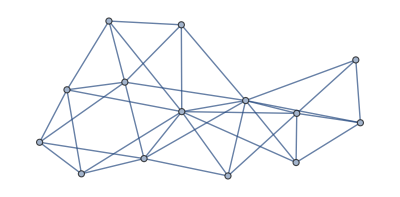

```mathematica
ReadGrof[65500]
```

```mathematica
Chromial[65500]
```

-558414 x+2744685 x^2-6110235 x^3+8196930 x^4-7419951 x^5+4799916 x^6-2288413 x^7+815833 x^8-217883 x^9+43122 x^10-6156 x^11+601 x^12-36 x^13+x^14

```mathematica
Det[Matt[3]]==1
```

-x1m3 x2m2 x3m1+x1m2 x2m3 x3m1+x1m3 x2m1 x3m2-x1m1 x2m3 x3m2-x1m2 x2m1 x3m3+x1m1 x2m2 x3m3==1

```mathematica
boega=With[{size=15},

Flatten[
Matt[size]/.Solve[
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
CacheChebychev[k],{k,1,78800(*58716*)}]
,k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]
];MatrixForm[boega]
```

678

Solve::svars: Equations may not give solutions for all "solve" variables.

(x1m1 | x1m2 | x1m3 | x1m4 | x1m5 | x1m6 | x1m7 | x1m8 | x1m9 | x1m10 | x1m11 | x1m12 | x1m13 | x1m14 | x1m15
x2m1 | x2m2 | x2m3 | x2m4 | x2m5 | x2m6 | x2m7 | x2m8 | x2m9 | x2m10 | x2m11 | x2m12 | x2m13 | x2m14 | x2m15
x3m1 | x3m2 | x3m3 | x3m4 | x3m5 | x3m6 | x3m7 | x3m8 | x3m9 | x3m10 | x3m11 | x3m12 | x3m13 | x3m14 | x3m15
-3/4-2 x2m1+3 x3m1 | 5/4-2 x2m2+3 x3m2 | -3/4-2 x2m3+3 x3m3 | 1/8-2 x2m4+3 x3m4 | -2 x2m5+3 x3m5 | -2 x2m6+3 x3m6 | -2 x2m7+3 x3m7 | -2 x2m8+3 x3m8 | -2 x2m9+3 x3m9 | -2 x2m10+3 x3m10 | -2 x2m11+3 x3m11 | -2 x2m12+3 x3m12 | -2 x2m13+3 x3m13 | -2 x2m14+3 x3m14 | -2 x2m15+3 x3m15
-13/8-6 x2m1+7 x3m1 | 3-6 x2m2+7 x3m2 | -25/16-6 x2m3+7 x3m3 | -6 x2m4+7 x3m4 | 1/16-6 x2m5+7 x3m5 | -6 x2m6+7 x3m6 | -6 x2m7+7 x3m7 | -6 x2m8+7 x3m8 | -6 x2m9+7 x3m9 | -6 x2m10+7 x3m10 | -6 x2m11+7 x3m11 | -6 x2m12+7 x3m12 | -6 x2m13+7 x3m13 | -6 x2m14+7 x3m14 | -6 x2m15+7 x3m15
-15/4-14 x2m1+15 x3m1 | 229/32-14 x2m2+15 x3m2 | -15/4-14 x2m3+15 x3m3 | 1/8-14 x2m4+15 x3m4 | -14 x2m5+15 x3m5 | 1/32-14 x2m6+15 x3m6 | -14 x2m7+15 x3m7 | -14 x2m8+15 x3m8 | -14 x2m9+15 x3m9 | -14 x2m10+15 x3m10 | -14 x2m11+15 x3m11 | -14 x2m12+15 x3m12 | -14 x2m13+15 x3m13 | -14 x2m14+15 x3m14 | -14 x2m15+15 x3m15
-491/64-30 x2m1+31 x3m1 | 15-30 x2m2+31 x3m2 | -487/64-30 x2m3+31 x3m3 | -30 x2m4+31 x3m4 | 5/64-30 x2m5+31 x3m5 | -30 x2m6+31 x3m6 | 1/64-30 x2m7+31 x3m7 | -30 x2m8+31 x3m8 | -30 x2m9+31 x3m9 | -30 x2m10+31 x3m10 | -30 x2m11+31 x3m11 | -30 x2m12+31 x3m12 | -30 x2m13+31 x3m13 | -30 x2m14+31 x3m14 | -30 x2m15+31 x3m15
-63/4-62 x2m1+63 x3m1 | 1991/64-62 x2m2+63 x3m2 | -63/4-62 x2m3+63 x3m3 | 7/64-62 x2m4+63 x3m4 | -62 x2m5+63 x3m5 | 3/64-62 x2m6+63 x3m6 | -62 x2m7+63 x3m7 | 1/128-62 x2m8+63 x3m8 | -62 x2m9+63 x3m9 | -62 x2m10+63 x3m10 | -62 x2m11+63 x3m11 | -62 x2m12+63 x3m12 | -62 x2m13+63 x3m13 | -62 x2m14+63 x3m14 | -62 x2m15+63 x3m15
-4057/128-126 x2m1+127 x3m1 | 63-126 x2m2+127 x3m2 | -2025/64-126 x2m3+127 x3m3 | -126 x2m4+127 x3m4 | 5/64-126 x2m5+127 x3m5 | -126 x2m6+127 x3m6 | 7/256-126 x2m7+127 x3m7 | -126 x2m8+127 x3m8 | 1/256-126 x2m9+127 x3m9 | -126 x2m10+127 x3m10 | -126 x2m11+127 x3m11 | -126 x2m12+127 x3m12 | -126 x2m13+127 x3m13 | -126 x2m14+127 x3m14 | -126 x2m15+127 x3m15
-255/4-254 x2m1+255 x3m1 | 32533/256-254 x2m2+255 x3m2 | -255/4-254 x2m3+255 x3m3 | 3/32-254 x2m4+255 x3m4 | -254 x2m5+255 x3m5 | 27/512-254 x2m6+255 x3m6 | -254 x2m7+255 x3m7 | 1/64-254 x2m8+255 x3m8 | -254 x2m9+255 x3m9 | 1/512-254 x2m10+255 x3m10 | -254 x2m11+255 x3m11 | -254 x2m12+255 x3m12 | -254 x2m13+255 x3m13 | -254 x2m14+255 x3m14 | -254 x2m15+255 x3m15
-65387/512-510 x2m1+511 x3m1 | 255-510 x2m2+511 x3m2 | -65363/512-510 x2m3+511 x3m3 | -510 x2m4+511 x3m4 | 75/1024-510 x2m5+511 x3m5 | -510 x2m6+511 x3m6 | 35/1024-510 x2m7+511 x3m7 | -510 x2m8+511 x3m8 | 9/1024-510 x2m9+511 x3m9 | -510 x2m10+511 x3m10 | 1/1024-510 x2m11+511 x3m11 | -510 x2m12+511 x3m12 | -510 x2m13+511 x3m13 | -510 x2m14+511 x3m14 | -510 x2m15+511 x3m15
-1023/4-1022 x2m1+1023 x3m1 | 261665/512-1022 x2m2+1023 x3m2 | -1023/4-1022 x2m3+1023 x3m3 | 165/2048-1022 x2m4+1023 x3m4 | -1022 x2m5+1023 x3m5 | 55/1024-1022 x2m6+1023 x3m6 | -1022 x2m7+1023 x3m7 | 11/512-1022 x2m8+1023 x3m8 | -1022 x2m9+1023 x3m9 | 5/1024-1022 x2m10+1023 x3m10 | -1022 x2m11+1023 x3m11 | 1/2048-1022 x2m12+1023 x3m12 | -1022 x2m13+1023 x3m13 | -1022 x2m14+1023 x3m14 | -1022 x2m15+1023 x3m15
-523999/1024-2046 x2m1+2047 x3m1 | 1023-2046 x2m2+2047 x3m2 | -2095831/4096-2046 x2m3+2047 x3m3 | -2046 x2m4+2047 x3m4 | 275/4096-2046 x2m5+2047 x3m5 | -2046 x2m6+2047 x3m6 | 77/2048-2046 x2m7+2047 x3m7 | -2046 x2m8+2047 x3m8 | 27/2048-2046 x2m9+2047 x3m9 | -2046 x2m10+2047 x3m10 | 11/4096-2046 x2m11+2047 x3m11 | -2046 x2m12+2047 x3m12 | 1/4096-2046 x2m13+2047 x3m13 | -2046 x2m14+2047 x3m14 | -2046 x2m15+2047 x3m15
-4095/4-4094 x2m1+4095 x3m1 | 16769453/8192-4094 x2m2+4095 x3m2 | -4095/4-4094 x2m3+4095 x3m3 | 143/2048-4094 x2m4+4095 x3m4 | -4094 x2m5+4095 x3m5 | 429/8192-4094 x2m6+4095 x3m6 | -4094 x2m7+4095 x3m7 | 13/512-4094 x2m8+4095 x3m8 | -4094 x2m9+4095 x3m9 | 65/8192-4094 x2m10+4095 x3m10 | -4094 x2m11+4095 x3m11 | 3/2048-4094 x2m12+4095 x3m12 | -4094 x2m13+4095 x3m13 | 1/8192-4094 x2m14+4095 x3m14 | x14m15
-33549907/16384-8190 x2m1+8191 x3m1 | 4095-8190 x2m2+8191 x3m2 | -33549335/16384-8190 x2m3+8191 x3m3 | -8190 x2m4+8191 x3m4 | 1001/16384-8190 x2m5+8191 x3m5 | -8190 x2m6+8191 x3m6 | 637/16384-8190 x2m7+8191 x3m7 | -8190 x2m8+8191 x3m8 | 273/16384-8190 x2m9+8191 x3m9 | -8190 x2m10+8191 x3m10 | 77/16384-8190 x2m11+8191 x3m11 | -8190 x2m12+8191 x3m12 | 13/16384-8190 x2m13+8191 x3m13 | -8190 x2m14+8191 x3m14 | 1/16384+36 x14m15+139194 x2m15-139229 x3m15)

```mathematica
ChebyBaseCoeffT[ChromaticPolynomial[JacobsThalGraph[8],x]]
```

{408149723/1024,-182379007/256,64234981/128,-69506615/256,226881423/2048,-17312451/512,1968101/256,-662283/512,162653/1024,-7095/512,209/256,-15/512,1/2048}

```mathematica
ChebyBaseCoeff[ChromaticPolynomial[JacobsThalGraph[5],x]]
```

{-347543/128,1019045/256,-207557/64,52821/32,-34867/64,60731/512,-4347/256,99/64,-21/256,1/512}

```mathematica
Table[ChebyshevU[k,x],{k,1,10}]
```

{2 x,-1+4 x^2,-4 x+8 x^3,1-12 x^2+16 x^4,6 x-32 x^3+32 x^5,-1+24 x^2-80 x^4+64 x^6,-8 x+80 x^3-192 x^5+128 x^7,1-40 x^2+240 x^4-448 x^6+256 x^8,10 x-160 x^3+672 x^5-1024 x^7+512 x^9,-1+60 x^2-560 x^4+1792 x^6-2304 x^8+1024 x^10}

```mathematica
Table[ChebyshevT[k,x],{k,1,10}]
```

{x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4,5 x-20 x^3+16 x^5,-1+18 x^2-48 x^4+32 x^6,-7 x+56 x^3-112 x^5+64 x^7,1-32 x^2+160 x^4-256 x^6+128 x^8,9 x-120 x^3+432 x^5-576 x^7+256 x^9,-1+50 x^2-400 x^4+1120 x^6-1280 x^8+512 x^10}

```mathematica
Chromial[5000]
```

-46656 x+205578 x^2-402165 x^3+463698 x^4-351567 x^5+184617 x^6-68689 x^7+18145 x^8-3341 x^9+409 x^10-30 x^11+x^12

```mathematica
RowConstr[length_,j_,val_]:=Fold[And,Table[Symbol["x" <>ToString[ j] <>"m" <> ToString[ i]]==val,{i,1,length}]]
```

```mathematica
RowConstr[12,1,0]
```

x1m1==0&&x2m1==0&&x3m1==0&&x4m1==0&&x5m1==0&&x6m1==0&&x7m1==0&&x8m1==0&&x9m1==0&&x10m1==0&&x11m1==0&&x12m1==0

```mathematica
457
```

```mathematica
SkewConst[length_,value_]:=Fold[And,Flatten[Table[Symbol["x" <>ToString[ i] <>"m" <> ToString[ j]]==value,{i,1,length},{j,i+1,length}]]]
```

```mathematica
boega2=With[{size=14},

Flatten[
Matt[size]/.Solve[(*
x3m3==3/2&&
x2m2==2&&
x1m1==0&&
x3m2==1&&
x2m1==1&&*)
SkewConst[size,1]&&
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
CacheChebychevT[k],{k,1,58716(*58716*)}]
,k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]
];MatrixForm[boega2]
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[$Aborted].

1

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

Solve::naqs: x1m2 == 1 && x1m3 == 1 && x1m4 == 1 && x1m5 == 1 && x1m6 == 1 && x1m7 == 1 && x1m8 == 1 && x1m9 == 1 && x1m10 == 1 && x1m11 == 1 && x1m12 == 1 && x1m13 == 1 && x1m14 == 1 && x2m3 == 1 && x2m4 == 1 && x2m5 == 1 && x2m6 == 1 && x2m7 == 1 && x2m8 == 1 && x2m9 == 1 && x2m10 == 1 && x2m11 == 1 && x2m12 == 1 && x2m13 == 1 && x2m14 == 1 && x3m4 == 1 && x3m5 == 1 && x3m6 == 1 && x3m7 == 1 && x3m8 == 1 && x3m9 == 1 && x3m10 == 1 && x3m11 == 1 && x3m12 == 1 && x3m13 == 1 && x3m14 == 1 && x4m5 == 1 && x4m6 == 1 && x4m7 == 1 && x4m8 == 1 && x4m9 == 1 && x4m10 == 1 && x4m11 == 1 && x4m12 == 1 && x4m13 == 1 && x4m14 == 1 && x5m6 == 1 && x5m7 == 1 && x5m8 == 1 && x5m9 == 1 && « 42 » is not a quantified system of equations and inequalities.

$Aborted

```mathematica
Det[boega2]
```

1/73786976294838206464(-x14m1-52667 x14m10-196560 x14m11-733589 x14m12-2737801 x14m13+3739875 x14m14+x14m2-17 x14m4-73 x14m5-269 x14m6-1008 x14m7-3779 x14m8-14113 x14m9+35112 x14m10 x3m1+131042 x14m11 x3m1+489060 x14m12 x3m1+1825200 x14m13 x3m1-2493258 x14m14 x3m1+2 x14m3 x3m1+12 x14m4 x3m1+48 x14m5 x3m1+180 x14m6 x3m1+674 x14m7 x3m1+2520 x14m8 x3m1+9408 x14m9 x3m1)

```mathematica
ChebyBaseCoeff[ChromaticPolynomial[ReadGrof[16],x]]
```

{72945/128,-26673/32,10651/16,-10335/32,3135/32,-597/32,555/256,-9/64,1/256}

```mathematica
ChebyBaseCoeff[ChromaticPolynomial[Rule2[ReadGrof[16],5<->6,4<->2],x]]
```

{-306039/128,897401/256,-183993/64,95037/64,-32015/64,57091/512,-4187/256,195/128,-21/256,1/512}

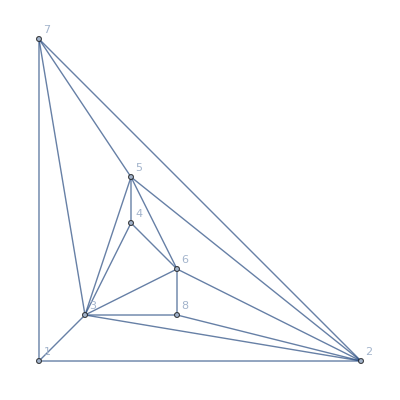

```mathematica
Graph[ReadGrof[16],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
boega=With[{size=14},

Flatten[
Matt[size]/.Solve[
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
CacheChebychev[k],{k,1,100000(*58716*)}]
,k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]
];MatrixForm[boega]
```

$Aborted

```mathematica
eded =Monitor[Table[Chromial[k],{k,1,300000}],k];Length[eded]
```